8.02 Mathematica Lesson 3
"Open/Close CoSet"

Click Enable Dynamics  in the right upper corner of the notebook before starting to work!

Click Evaluation in the tool bar and then click Evaluate Notebook to evaluate all the variables and the functions in the code that are in the notebook. This will take about 30 seconds. 

After reading this Mathematica notebook, you will be able to: 1)  evaluate a simple line integral,  2) calculate the electric potential of a continuous charge distribution, and 3) plot equipotentials 

Tutorial + Assignment: The tutorial is divided in three parts. Each part is followed by a problem. Reading the tutorial and interacting with the pieces of code in it will prepare you to do the problems.

Save my work: After typing one or several lines of code in your solution you can click “Save my work and Give Feedback”. “Save my work” does NOT save the changes done in the notebook. It locks your answer into the notebook by creating gray cells that can not be edited anymore. If you are not pleased with your answer you will be able to type a new solution as many times as you want.  

Access Solution: Note that after clicking “Save my work and Give Feedback” for the first time you will be able to view the solution.  This is done for pedagogical purposes. There are many ways of writing a code so the posted solution might be different from yours. 

Save: Before closing the notebook make sure that you have saved your changes by clicking Save from the File menu. If you do not save the changes the grader will not see your work and you will not receive a grade.  (Saving a file frequently is always  a good practice!)

Upload to Stellar: Do not forget to upload your notebook to Stellar!!

graphics initialization (modifying options)

(*we probably won't need these*)
(*r=1.7;
radius = .04(*.4*);
inradius = .05;
radiusTWO = .1;
outerchg =2;*)
Clear[x,y,z];
Clear[PointChargeAtOriginField,x,y,z,charg];

(*changing default options for ContourPlot3D. We could even modify the d.v.'s i*)
Unprotect[ContourPlot3D];
Options[ContourPlot3D]=
{
	(*modified options*)
	PlotPoints→(*17*)26,(*Mesh→All,*)MaxRecursion→0,Mesh→None,
	ColorFunction→"TemperatureMap",ViewPoint→{1.3,-2.4,-31.}(*need to use ViewMatrix*),Contours→Range[-7,7],
	
	(*original options*)
	AlignmentPoint→Center,AspectRatio→Automatic,AutomaticImageSize→False,Axes→True,AxesEdge→Automatic,AxesLabel→None,AxesOrigin→Automatic,AxesStyle→{},Background→None,BaselinePosition→Automatic,BaseStyle→{},BoundaryStyle→GrayLevel[0],Boxed→True,BoxRatios→{1,1,1},BoxStyle→{},ClipPlanes→None,ClipPlanesStyle→Automatic,ColorFunctionScaling→True,ColorOutput→Automatic,ContentSelectable→Automatic,ContourStyle→GrayLevel[1],ControllerLinking→Automatic,ControllerMethod→Automatic,ControllerPath→Automatic,CoordinatesToolOptions→Automatic,DisplayFunction:>$DisplayFunction,Epilog→{},Evaluated→Automatic,EvaluationMonitor→None,FaceGrids→None,FaceGridsStyle→{},FormatType:>TraditionalForm,ImageMargins→0.,ImagePadding→All,ImageSize→Automatic,ImageSizeRaw→Automatic,LabelStyle→{},Lighting→Automatic,MaxRecursion→Automatic,Mesh→Automatic,MeshFunctions→{#1&,#2&,#3&},MeshShading→None,MeshStyle→Automatic,Method→Automatic,NormalsFunction→Automatic,PerformanceGoal:>$PerformanceGoal,PlotLabel→None,PlotLegends→None,PlotPoints→Automatic,PlotRange→{Full,Full,Full,Automatic},PlotRangePadding→Automatic,PlotRegion→Automatic,PlotTheme:>$PlotTheme,PreserveImageOptions→Automatic,Prolog→{},RegionFunction→(True&),RotationAction→"Fit",SphericalRegion→False,TargetUnits→Automatic,TextureCoordinateFunction→Automatic,TextureCoordinateScaling→Automatic,Ticks→Automatic,TicksStyle→{},TouchscreenAutoZoom→False,ViewAngle→Automatic,ViewCenter→Automatic,ViewMatrix→Automatic,ViewProjection→Automatic,ViewRange→All,ViewVector→Automatic,ViewVertical→{0,0,1},WorkingPrecision→MachinePrecision
};
Protect[ContourPlot3D];

Unprotect[ContourPlot];
Options[ContourPlot]=
{
	(*modified options*)
	ContourLabels→True,Contours→16,
	
	(*original options*)
	Sequence@@Options[ContourPlot]
};
Protect[ContourPlot];

(*Unprotect[SliceVectorPlot3D];
Options[SliceVectorPlot3D]=
{
	(*original options*)
	Sequence@@Options[SliceVectorPlot3D],
	
	(*modified options*)
	VectorStyle→Arrowheads[.01], ViewPoint→{.1,.1,-10},VectorScale→{Medium, 0.6, (*Sqrt@*)Sqrt[#5]&(*Automatic*)},(*Boxed→False,*)
	Axes→True, PlotStyle→Opacity[0.1],VectorPoints→17(*RandomReal[{-2,2},{2,888}]*),AxesLabel→Automatic
};
Protect[SliceVectorPlot3D];*)
SetOptions[SliceVectorPlot3D,ViewPoint→{.1,.1,10}];
SetOptions[SliceVectorPlot3D,VectorScale→{Medium, 0.6, (*Sqrt@*)1/(#1^2+#2^2+#3^2)^.3&(*Automatic*)}];
SetOptions[SliceVectorPlot3D,Axes→True];
SetOptions[SliceVectorPlot3D,PlotStyle→Opacity[0.1]];
SetOptions[SliceVectorPlot3D,VectorPoints→16];
SetOptions[SliceVectorPlot3D,AxesLabel→Automatic];
SetOptions[SliceVectorPlot3D,ImageSize→Large];
SetOptions[SliceVectorPlot3D,VectorStyle→Arrowheads[.01]];

SetOptions[VectorPlot,VectorStyle→Arrowheads[.02]];
SetOptions[VectorPlot,VectorScale→{Medium, 0.6, (*Sqrt@*)1/(#1^2+#2^2)^.3&(*Automatic*)}];
SetOptions[VectorPlot,VectorPoints→16];

Unprotect[VectorPlot3D];
Options[VectorPlot3D]=
{
	(*modified options*)
	VectorStyle→Arrowheads[.01], ViewPoint→{11,-20,4}(*need to use ViewMatrix!*),VectorScale→{Automatic,Automatic,Function[If[1/(#1^2+#2^2+#3^2)>2,None,1/(#1^2+#2^2+#3^2)]]}(*{Small, .6, (*Sqrt@*)(*1/*)1/(#1^2+#2^2+#3^2)^.3&(*Automatic*)}*),(*Boxed→False,*)
Axes→True, (*PlotStyle→Opacity[0.3],*)VectorPoints→10(*RandomReal[{-2,2},{2,888}]*),AxesLabel→{"x","y","z"},
	(*original options*)
	Sequence@@Options[VectorPlot3D]
};
Protect[VectorPlot3D];
SetOptions[VectorPlot3D,ImageSize→Large];

Clear[x,y,z];

Electric Potential of a finite rod
"Open/Close Chapter"

Change of Electric Potential knowing the electric field
"Open/Close Section"

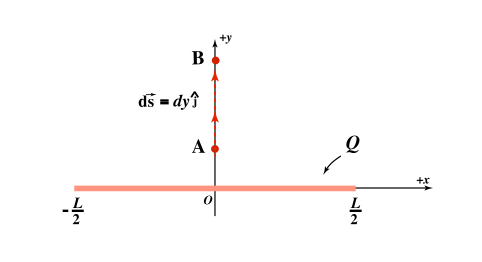
Consider a wire of length L = 2 m uniformly charged with a charge Q = 2x10^-9 C. The wire is in the x-axis centered at the origin of the coordinate system. The goal of the problem is to calculate the change of electric potential between the points A ={ 0, 1} and B = {0,3}  shown in the figure below. 
-Graphics-

The change of electric potential between points A and B  is given by :

              (eq. 1)

where E⃗  is the electric field of the rod and d s⃗  is an element of the path between points A and B. In the following example the chosen path is along the y-axis, therefore d s⃗=dy ĵ.

In Lesson 2 we calculated the electric field of the finite rod by integrating the “eFieldFunc[...]” defined in Lesson 1. We repeat the steps below so we can use the results to calculate the change of electric potential (this can take a few seconds.)

k = 9*10^9 ;(* the electric constant.  [k] = N.m^2.C^(-2)  *)

eFieldFunc[sourcePoint_, fieldPoint_, charge_] := 
k*charge*(fieldPoint-sourcePoint )/EuclideanDistance[fieldPoint, sourcePoint]^3

rodCharge = 2* 10^(-9); (* C *)
rodLength = 2 ;    (* m *)
lambda = rodCharge/rodLength;    (* linear charge density C/m^3 *)

rodField=
Integrate[
eFieldFunc[{xs,0},{x,y},lambda], 
{xs,-1,1},
Assumptions→(Element[xs,Reals]&&Element[x,Reals] && Element[y,Reals] && y!=0 && x!=0)
]

{-(9 (√(1-2 x+x^2+y^2)-√(1+2 x+x^2+y^2)))/(√(1-2 x+x^2+y^2) √(1+2 x+x^2+y^2)),(9 (√(1-2 x+x^2+y^2)+x √(1-2 x+x^2+y^2)+√(1+2 x+x^2+y^2)-x √(1+2 x+x^2+y^2)))/(y √(1-2 x^2+x^4+2 y^2+2 x^2 y^2+y^4))}

Note: Notice the semicolons “;” at the end of some of the statements in the code above. A semicolon at the end of an expression does not allow the display of the output of that expression when  “Evaluate Notebook” is clicked. In the cell above, the semicolons are at the end of the definitions of the constants  therefore we will not be able to see their numerical values after the notebook evaluation. On the other hand, there is not a semicolon after the definition of  “rodField” therefore we will be able to see the output of this expression. After the definition of a function, example “eField”  above, there is no need to add a semicolon.

To calculate the line integral in (eq. 1) we need to do the dot product between E⃗ and ⅆ s⃗.  Because we have picked the path to be along the y-axis the element of path is d s⃗=dy ĵ, therefore the dot product between E⃗ and ⅆ s⃗ becomes:   E⃗. ⅆ s⃗=E⃗. (dy ĵ) = E_y dy.

 In Mathematica, the dot product of vectors  A and B is done using the Dot[_ , _] function: Dot[ A, B]. A short cut is to use the period/decimal button:  A.B,  as done below:
 
- The unit vector  ĵ is expressed as ĵ = {0, 1},  
- The rod’s electric field is  E⃗= rodField, 
- The y-component of the e-field is  E_y= E⃗. ĵ = rodField .  {0,1}  =fieldY
- The dot product between E⃗ and ⅆ s⃗ becomes:   E⃗. ⅆ s⃗=E⃗. (dy ĵ) = E_y dy.

fieldY= rodField.{0,1}  (* y-component of the rod's electric field *)

(9 (√(1-2 x+x^2+y^2)+x √(1-2 x+x^2+y^2)+√(1+2 x+x^2+y^2)-x √(1+2 x+x^2+y^2)))/(y √(1-2 x^2+x^4+2 y^2+2 x^2 y^2+y^4))

The expression above is the y-component of the rod’s electric field at any {x,y} point is the plane. To calculate the line integral  ∫_A^B E⃗. ⅆ s⃗ we only need to know E_y at the points along the path. For that purpose, we substitute x = 0 in the expression of the y-component of the electric field using  the function ReplaceAll[ ] as shown below:

fieldYAlongYaxis=ReplaceAll[fieldY,{x -> 0}]

(18 √(1+y^2))/(y √(1+2 y^2+y^4))

Note: We emphasize here that the y-component of the rod’s electric field, “fieldY”,  is a function of x and y, therefore we replace the value of x by 0 using {x -> 0} after the expression of fieldY inside the ReplaceAll[ ] function.

Now we are ready to calculate  -∫_A^B E⃗. ⅆ s⃗ to find the difference in potential. If point A = {0,1} and point B={0,3}, the difference in potential between A and B is obtained using the Integrate[]  function. 

In the box below deltaV = V(B) - V(A) = -∫_(y=1)^(y=3) E_y dy

deltaVAB = -Integrate[fieldYAlongYaxis,{y,1,3},(Assumptions→Element[y,Reals])]

-18 (-ArcSinh[1/3]+ArcSinh[1])

Recall: 
1. {y, 1, 3} indicates the limits of integration: 1< y < 3.  
2. The dy is already considered in the Integrate[ ] function.
3. To tell Mathematica that that y is a real number  we need to type   (Assumptions→Element[y,Reals] after the last argument of the function Integrate[].

N[deltaVAB]

-9.97062

Note:  N[ ] gives the numerical value of the expression inside the square brackets [ ] . In the box above, N[deltaV] gives the numerical value of deltaV.

Problem 1 - Part A - Change of electric potential along a new path.
"Open/Close Section""Create Scratchpad""Save Work and Give Feedback"

Consider the same rod as the one described in the tutorial. Calculate V(D) - V(C), the change of electric potential between the points C = {4,0} and D = {8,0}.

Work saved at Sun 4 Mar 2018 20:11:48

```mathematica
fieldX = rodField.{1,0}
```

-(9 (√(1-2 x+x^2+y^2)-√(1+2 x+x^2+y^2)))/(√(1-2 x+x^2+y^2) √(1+2 x+x^2+y^2))

```mathematica
fieldXAlongXaxis=ReplaceAll[fieldX,{y -> 0}]
```

-(9 (√(1-2 x+x^2)-√(1+2 x+x^2)))/(√(1-2 x+x^2) √(1+2 x+x^2))

```mathematica
deltaVAB = -Integrate[fieldXAlongXaxis,{x,4,8},(Assumptions->Element[x,Reals])]
```

-9 Log[35/27]

```mathematica
N[deltaVAB]
```

-2.3356

After you view the teacher's solution, you can incorporate anything you learned into your work here if you would like to do so.

```mathematica
fieldX = rodField.{1,0}
```

-(9 (√(1-2 x+x^2+y^2)-√(1+2 x+x^2+y^2)))/(√(1-2 x+x^2+y^2) √(1+2 x+x^2+y^2))

```mathematica
fieldXAlongXaxis=ReplaceAll[fieldX,{y -> 0}]
```

-(9 (√(1-2 x+x^2)-√(1+2 x+x^2)))/(√(1-2 x+x^2) √(1+2 x+x^2))

```mathematica
deltaVAB = -Integrate[fieldXAlongXaxis,{x,4,8},(Assumptions->Element[x,Reals])]
```

-9 Log[35/27]

```mathematica
N[deltaVAB]
```

-2.3356

Solution to Problem 1- Part A
"Open/Close Section""Access Solution"

We pick the path to be along the x-axis,  d s⃗=dx î, therefore 

V(D)-V(C) = -∫_C^D E⃗. (ⅆxî)=-∫_(x=4)^(x=8) E_x dx.

Calculate the x-component of the electric field by doing the dot product between rodFiled and  î ={1,0}:

fieldX=rodField.{1,0}

-(9 (√(1-2 x+x^2+y^2)-√(1+2 x+x^2+y^2)))/(√(1-2 x+x^2+y^2) √(1+2 x+x^2+y^2))

Evaluate the x-component of the electric field along the path of integration which is the x-axis,

fieldXAlongXaxis = ReplaceAll[fieldX,{y -> 0}]

-(9 (√(1-2 x+x^2)-√(1+2 x+x^2)))/(√(1-2 x+x^2) √(1+2 x+x^2))

Integrate the x-component of the e-field between x = 4 to x = 8 using Integrate[]:

deltaVCD = -Integrate[fieldXAlongXaxis,{x,4,8},(Assumptions→Element[y,Reals])]

-9 Log[35/27]

Use N[ ] to view the value of the expression deltaVnew

N[deltaVCD]

-2.3356

Use the button above to start viewing the solution

Change of Electric Potential by integration over the source
"Open/Close Section"

We have shown in class that the electric potential produced by a point charge q placed at (r⃗)_S is given by:
     (eq. 2)
where  (r⃗)_P is a generic point in space where we want to calculate the electric potential.

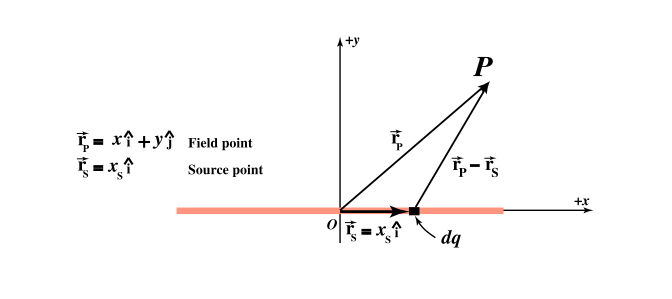
For a continuous charge distribution, like the example of the rod, the electric potential at a point P with reference at infinity can be obtained as the superposition of the potential produced by each infinitesimal charge dq at that point. 
-Graphics-
   (eq. 3)

In the piece of code below we define the expression “rodPotential”, which  performs the integral in (eg. 3), Recall that dq = λ dx_S. Because the Integrate[] function incorporates the dx_S, we only use λ  = Q/L = 10^-9 C/m inside Integrate[ ] .

rodCharge = 2* 10^(-9);   (* C *)
rodLength = 2;   (* m *)
lambda = rodCharge/rodLength ;(* linear charge density C/m *)

rodPotential=
Integrate[
k*lambda/Sqrt[(x-xs)^2+y^2], 
{xs,-rodLength/2,rodLength/2},
Assumptions→(Element[xs,Reals]&&Element[x,Reals] && Element[y,Reals] && y!=0 )
]

9 Log[(1+x+√((1+x)^2+y^2))/(-1+x+√((-1+x)^2+y^2))]

Note. “rodPotential” is a function of {x,y}. We can check the result of the rod’s electric potential obtained above with the result obtained in the first part of the tutorial where we calculated  deltaVAB = V(B) - V(A) = -9.97062 J/C. In the code below we will calculate the change of electric potential following the three operations shown below:

1. Replace {x→0,y→3} in rodPotential to obtain the electric potential at point B = {0,3}: V(B)
2. Replace {x→0,y→1} in rodPotential to obtain the electric potential at point A = {0,1}: V(A)
3. Do the difference deltaVABnew = V(B)-V(A)

deltaVABnew = ReplaceAll[rodPotential,{x→0,y→3}]-ReplaceAll[rodPotential,{x→0,y→1}]

-9 Log[(1+√2)/(-1+√2)]+9 Log[(1+√10)/(-1+√10)]

Use N[ ] to compare the numerical values of deltaVABnew and deltaVAB calculated in the first part of the tutorial (we obtained N[deltaVAB] =  -9.97062186 (J/C) )

N[deltaVABnew]

-9.97062

We obtained the same result!

Problem 1- Part B 
"Open/Close Section""Create Scratchpad""Save Work and Give Feedback"

Use the expression rodPotential obtained in the second part of the tutorial to calculate V(D) - V(C), the change of electric potential between  the points C = {4,0} and D = {8,0}. Compare your result with result obtained in Problem 1 - A.

Work saved at Sun 4 Mar 2018 20:15:26

```mathematica
deltaVCDnew = ReplaceAll[rodPotential,{x->8,y->0}]-ReplaceAll[rodPotential,{x->4,y->0}]
```

9 Log[9/7]-9 Log[5/3]

```mathematica
N[deltaVCDnew]
```

-2.3356

After you view the teacher's solution, you can incorporate anything you learned into your work here if you would like to do so.

```mathematica
deltaVCDnew = ReplaceAll[rodPotential,{x->8,y->0}]-ReplaceAll[rodPotential,{x->4,y->0}]
```

9 Log[9/7]-9 Log[5/3]

```mathematica
N[deltaVCDnew]
```

-2.3356

Solution to Problem 1- Part B
"Open/Close Section""Access Solution"

We use the expression rodPotential[ ] , the rod’s electric potential  with reference at infinity,  obtained in the second part of the tutorial to:

1)  Calculate the electric potential at point D = {8,0}, use  ReplaceAll[ rodPotential, {x→8,y→0}]
2)  Calculate the electric potential at point C = {4,0}, use  ReplaceAll[ rodPotential, {x→4,y→0}]
3)  Calculate the difference deltaVCDnew = V(D) - V(C)

potentialD = ReplaceAll[rodPotential, {x→8,y→0}]
potentialC = ReplaceAll[rodPotential, {x→4,y→0}]
deltaVCDnew= potentialD- potentialC
N[deltaVCDnew]

9 Log[9/7]

9 Log[5/3]

9 Log[9/7]-9 Log[5/3]

-2.3356

Compare N[deltaVCD] and N[deltaVnew]

N[deltaVCDnew]-N[deltaVCD]

8.88178×10^-16

The difference between both results is zero.

Use the button above to start viewing the solution

Equipotentials of a Point Charge
"Open/Close Section"

Consider a point charge Q = 2.10^-9 C at the origin of the coordinate system. Its electric potential with reference at infinity is given by:

(eq. 4)

An equipotential surface is defined as those points in space with the same value of electric potential. As a consequence, the electric field is perpendicular to the surface at any on it. We will plot the equipotential surface in the xy plane. The graphic function to plot equipotentials in 2D is ContourPlot[ ] .

charge = 2 * 10^(-9)    (* C *)
k = 9*10^9   (* the electric constant.  [k] = N.m^2.C^(-2)  *)
ContourPlot[ k*charge/Sqrt[x^2+y^2],{x,-2,2},{y,-2,2}, ContourLabels→None]

1/500000000

9000000000

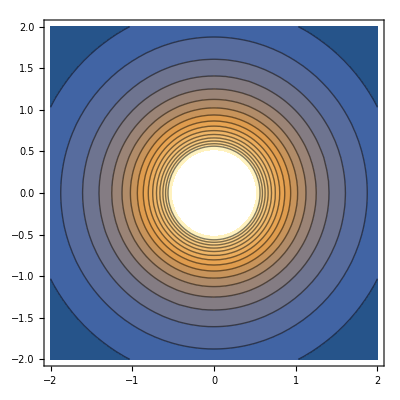

Note 1. we have set  the x and y axis to be between -2 and 2 in the ContourPlot[ ] .
Note 2. the option ContourLabels→None in the ContourPlot[ ]  removes the numbers labeling each line. We have done that for clarity.

We can also plot together the electric field lines and the equipotential lines using Show[ ] as follows

Show[
ContourPlot[ k*charge/Sqrt[x^2+y^2],{x,-2,2},{y,-2,2}, ContourLabels→None],
StreamPlot[eFieldFunc[{0,0},{x,y},charge],{x,-2,2},{y,-2,2}, StreamStyle→RGBColor[.1,.8,.3]]
]

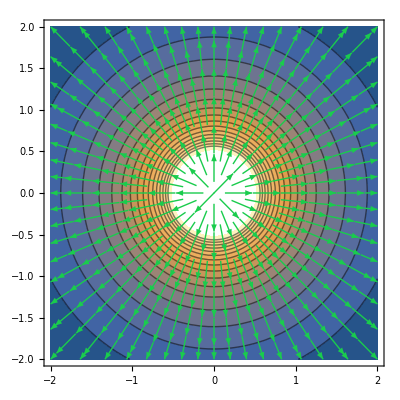

Note 1. Inside Show[ ] the graphic functions ContourPlot[ ]  and StreamPlot[ ] are separated by a comma.
Note 2. In StreamPlot[ ] we change the color of the e-field lines to green using the option StreamStyle→RGBColor[.1,.8,.3].

Problem 1- Part C - Equipotentials of the finite Rod 
"Open/Close Section""Create Scratchpad""Save Work and Give Feedback"

For the finite rod in this notebook, do a plot of the equipotential lines. In the same plot, draw the electric field vectors.

Work saved at Sun 4 Mar 2018 20:18:24

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

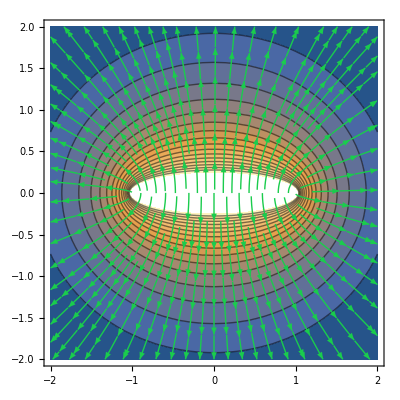

```mathematica
Show[
ContourPlot[ rodPotential,{x,-2,2},{y,-2,2}, ContourLabels->None],
StreamPlot[rodField,{x,-2,2},{y,-2,2}, StreamStyle->RGBColor[.1,.8,.3]]
]
```

After you view the teacher's solution, you can incorporate anything you learned into your work here if you would like to do so.

```mathematica
Show[
ContourPlot[ rodPotential,{x,-2,2},{y,-2,2}, ContourLabels->None],
StreamPlot[rodField,{x,-2,2},{y,-2,2}, StreamStyle->RGBColor[.1,.8,.3]]
]
```

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

-Graphics-

Solution to Problem 1- Part C
"Open/Close Section""Access Solution"

To draw the equipotential lines we use ContourPlot[ ] for the electric potential of the finite rod calculated in the second part of the tutorial “rodPotential”.  For the vector plot we use VectorPlot[ ] to plot the rodField function evaluated in the first part of the tutorial. Use Show[ ] to plot the equipotential lines and the e-field vectors in the same plot.

ContourPlot[rodPotential, {x,-3,3},{y,-3,3}, ContourLabels→None]

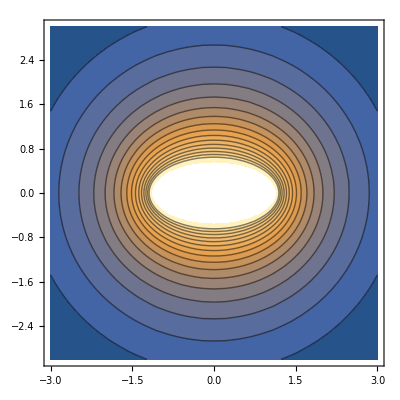

Use StreamPlot[ ] to draw the electric field lines of the “rodField” expression calculated in the first part of the tutorial

StreamPlot[rodField,{x,-2,2},{y,-2,2}, StreamStyle→RGBColor[.1,.8,.3]]

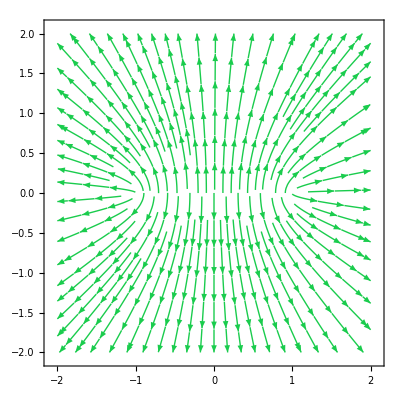

Use StreamPlot[ ] and ContourPlot[ ] separated by a comma inside Show[ ] to view both plots.

Show[ 
ContourPlot[rodPotential, {x,-2,2},{y,-2,2},ContourLabels→None ], StreamPlot[rodField,{x,-2,2},{y,-2,2}, StreamStyle→RGBColor[.1,.8,.3]]
]

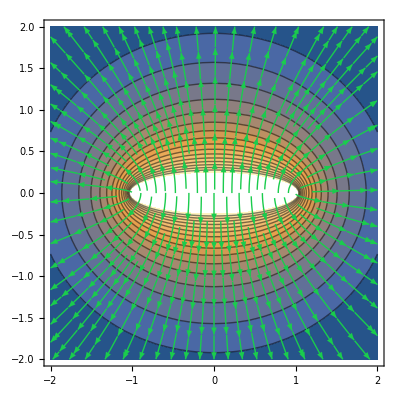

Use the button above to start viewing the solution